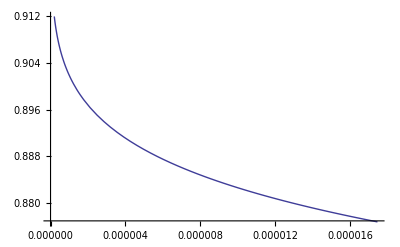

```mathematica
func[θB_,x0_,am_]:=NIntegrate[ArcTan[x0/Sqrt[w^2+am^2]]*4/Sqrt[w^2+am^2],{w,0,θB}]
norm[am_]:=1/(2π)(NIntegrate[Sin[a]/(a^2+am^2),{a,0,π/2}])^-1

Plot[norm[a]*func[10*π/180,90*π/180,a],{a,0,0.001*π/180}]
```